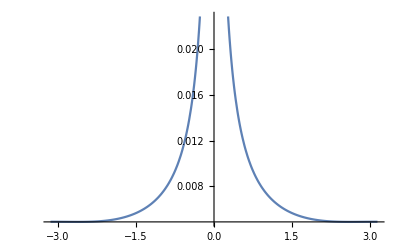

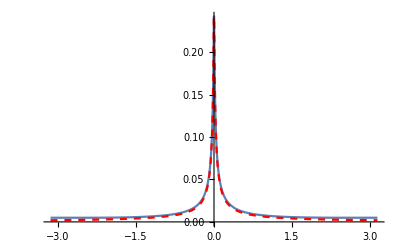

powspectth1overf.csv

powspectth1overfapprox.csv

omvecth.csv

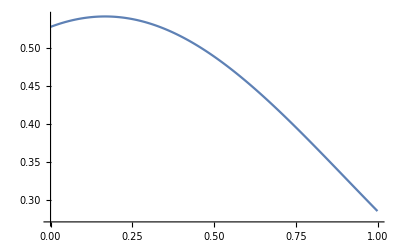

histth.csv

xvecth.csv

```mathematica
Clear["Global`*"];
(*Solving for the delta *)
r = 1.2;
sigma = Sqrt[2.1];
sigmat = Sqrt[0.02];
start = (1-1/r)^2 +0.1;
sol = FindRoot[1/(√(2 π) r^2)(ⅇ^(-(-1+1/r)^2/(2 q sigma^2)) √q (-1+r) r sigma-ⅇ^(-1/(2 q r^2 sigma^2)) √q r (-1+2 r) sigma-√(π/2) (1+r (-2+r+q r sigma^2)) Erf[(-1+1/r)/(√2 √q sigma)]+√(π/2) (1+r (-2+r+q r sigma^2)) Erf[1/(√2 √q r sigma)])+1/2 Erfc[1/(√2 √q r sigma)]==q,{q, start}];

q0 = q/.sol;

f[x_]:= 1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)]HeavisideTheta[1-x] ;

phi =(√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2));
powapprox[w_]:= phi sigmat^2/(1+Pi Abs[ w]/(2 r phi)f[0]-phi sigma^2 ) ;(*sigmat^2 phi^2/(phi(1-phi sigma^2) + w Pi f[0]/r);*)
av[w_]:= NIntegrate[f[x] (r x)^2/Abs[(r x) + Exp[I w]-1]^2,{x,0,1}];
pow[w_]:=  sigmat^2/(1/av[w] - sigma^2);


Plot[pow[w], {w, -Pi,Pi}]
xmin = -Pi;
xmax = Pi;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = pow[xvec];
histvecapprox = powapprox[xvec];
plt1 = ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All];
plt2 =  ListLinePlot[Transpose[{xvec,histvecapprox}],PlotRange->All, PlotStyle->{Red, Dashed}];
Show[plt1, plt2]

SetDirectory[NotebookDirectory[]];
Export["powspectth1overf.csv",N[histvec]]
Export["powspectth1overfapprox.csv",N[histvecapprox]]
Export["omvecth.csv",N[xvec]]



xmin = 0;
xmax = 1;
numx = 1000;
xvec = Table[x,{x,xmin,xmax,(xmax-xmin)/(numx-1)}];
histvec = f[xvec];
ListLinePlot[Transpose[{xvec,histvec}],PlotRange->All]

Export["histth.csv",N[histvec]]
Export["xvecth.csv",N[xvec]]
```

```mathematica
Clear["Global`*"];
Integrate[1/Sqrt[2Pi q0 sigma^2] Exp[-(x-(1-1/r))^2/(2sigma^2q0)],{x, 0,1}]
```

(√q0 sigma (-Erf[(-1+1/r)/(√2 √q0 sigma)]+Erf[1/(√2 √q0 r sigma)]))/(2 √(q0 sigma^2))

```mathematica
N[Exp[-0.4]]
```

0.67032